## Define constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.210(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
(*pp210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210a.csv"];
pp210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210b.csv"];*)
```

```mathematica
pp210a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp210a.csv"];
pp210b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp210b.csv"];
```

```mathematica
pp210a=Transpose[{pp210a[[All,1]],pp210a[[All,2]]+I*pp210a[[All,3]]}];
pp210b=Transpose[{pp210b[[All,1]],pp210b[[All,2]]+I*pp210b[[All,3]]}];
```

```mathematica
θpp210=Transpose[{pp210a[[All,1]],(pp210a[[All,2]]+pp210b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp210=θtoq/@θpp210;
```

```mathematica
(*pn210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn210a.csv"];
pn210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn210b.csv"];*)
```

```mathematica
pn210a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn210a.csv"];
pn210b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn210b.csv"];
```

```mathematica
pn210a=Transpose[{pn210a[[All,1]],pn210a[[All,2]]+I*pn210a[[All,3]]}];
pn210b=Transpose[{pn210b[[All,1]],pn210b[[All,2]]+I*pn210b[[All,3]]}];
```

```mathematica
θpn210=Transpose[{pn210a[[All,1]],(pn210a[[All,2]]+pn210b[[All,2]])/2}];
```

```mathematica
pn210=θtoq/@θpn210;
```

```mathematica
NN210=(pp210+pn210)/2;
```

```mathematica
f=Interpolation[NN210];
```

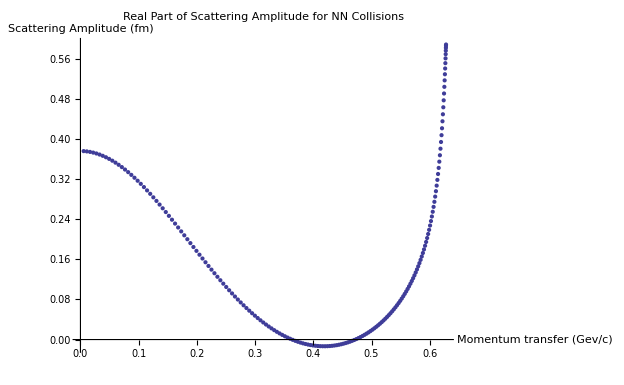

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Re[NN210[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

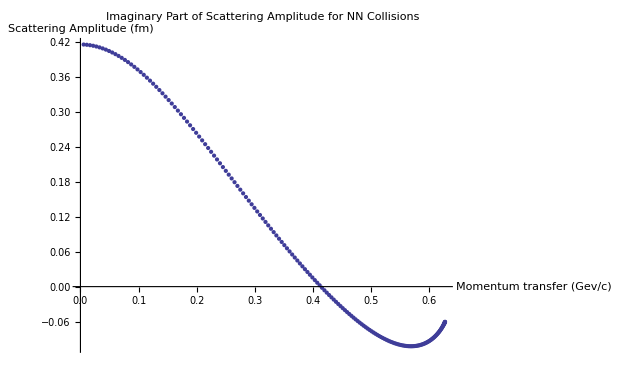

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Im[NN210[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

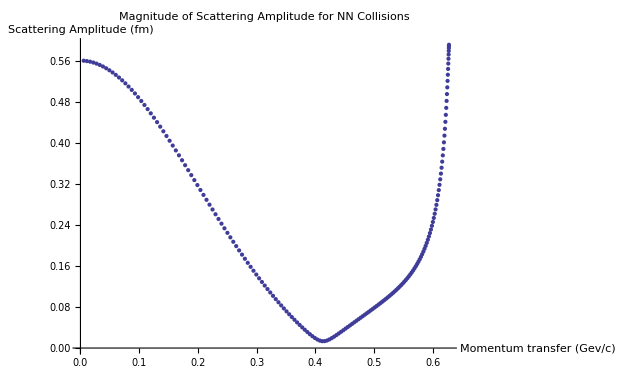

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Abs[NN210[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

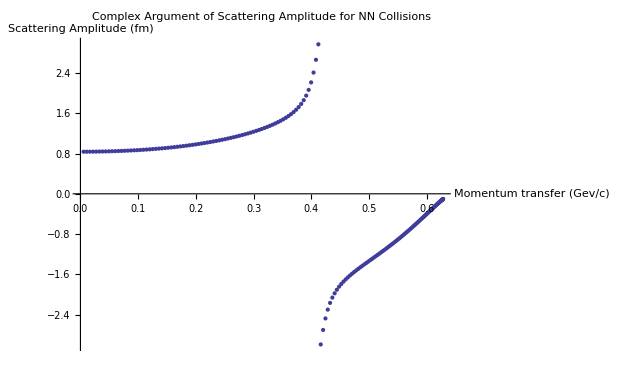

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Arg[NN210[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→0.562662,βre→14.4438}

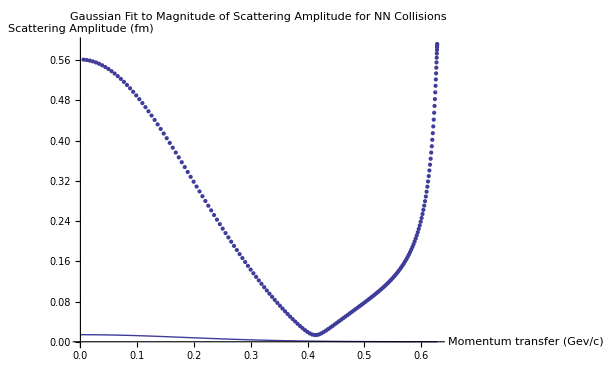

```mathematica
Npts=50;
FindFit[Transpose[{NN210[[1;;Npts,1]],Abs[NN210[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[κ a/(4 Pi) Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN210[[All,1]],Abs[NN210[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->All]
```

```mathematica
(4.18-I 2.70) Exp[-(16-I 5.66) q^2]/(2 I κ)
```

{ρ→0.916394,βim→-3.97743}

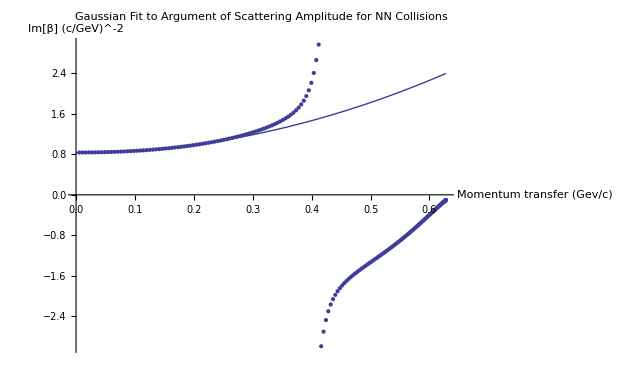

```mathematica
FindFit[Transpose[{NN210[[1;;Npts,1]],Arg[NN210[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN210[[All,1]],Arg[NN210[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Im[β] (c/GeV)^-2"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.5626620954511277&&ρ==0.9163935163116479,{σ,ρ}]
```

{{σ→3.27607,ρ→0.916394}}

Fitted parameters:

```mathematica
σ=3.2760668043032632;
ρ=0.9163935163116479;
β=14.4437913447594-3.977429080580476 I;
```

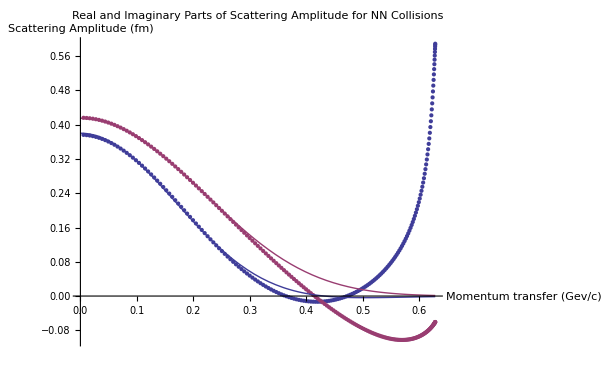

```mathematica
Show[ListPlot[Transpose[{NN210[[All,1]],Re[NN210[[All,2]]]}]],ListPlot[Transpose[{NN210[[All,1]],Im[NN210[[All,2]]]}],PlotStyle->ColorData[1,2]],Plot[{Re[κ/ℏc σ (ρ+I)/(4 Pi) Exp[-β q^2]],Im[κ/ℏc σ (ρ+I)/(4 Pi) Exp[-β q^2]]},{q,0,2 κ}],PlotRange->All,PlotLabel->"Real and Imaginary Parts of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

## Glauber

```mathematica
σ1=σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

0.269799-0.138098 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

125.188

```mathematica
ρ0[q_]:=Exp[-B q^2]
```

## Compare exact eikonal potential with approximation

InterpolatingFunction::dmval: Input value {0.0000128285} lies outside the range of data in the interpolating function. Extrapolation will be used.

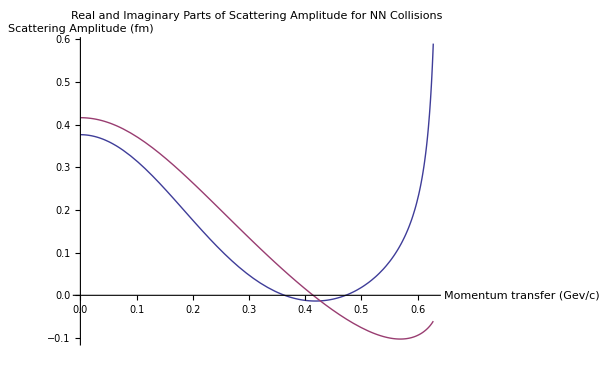

```mathematica
Plot[{Re[f[q]],Im[f[q]]},{q,0,2 κ},PlotLabel->"Real and Imaginary Parts of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

Below I interpolate Γ from b=1 c/GeV to 1000 c/GeV for faster evaluation.

```mathematica
G[b_]:=I/κ NIntegrate[BesselJ[0,b q] f[q]/ℏc q,{q,0,2 κ}]
```

```mathematica
Γ=Interpolation[Table[{b,G[b]},{b,0,1000}]];
```

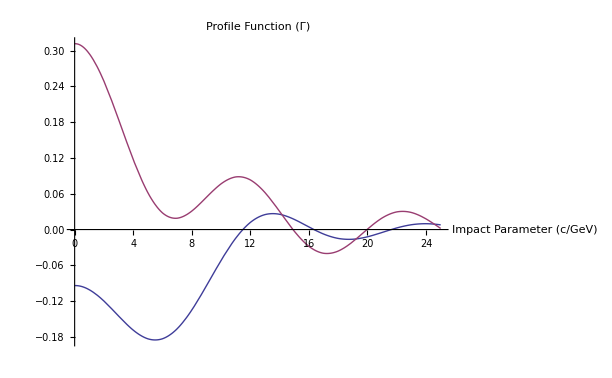

```mathematica
Plot[{Re[Γ[b]],Im[Γ[b]]},{b,0,25},PlotRange->All,PlotLabel->"Profile Function (Γ)",AxesLabel->{"Impact Parameter (c/GeV)",""}]
```

As it turns out, since Γ is a Fourier transform of f and U is (almost) an inverse Fourier transform of Γ, U is very close to being a constant multiple of f.

```mathematica
Utemp[q_]:=2 Pi I NIntegrate[b BesselJ[0,b q] Log[1-Γ[b]],{b,0,1000}]
```

```mathematica
interp=Interpolation[Table[{q,Utemp[q]},{q,0,.62,.01}]];
U[q_]:=Piecewise[{{interp[q],q<2 κ},{0,q≥2 κ}}]
```

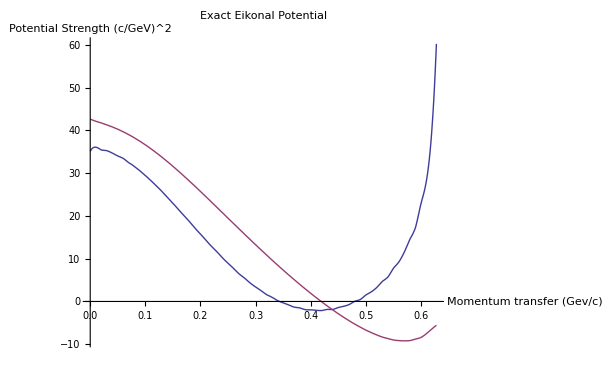

```mathematica
Plot[{Re[U[q]],Im[U[q]]},{q,0,2 κ},PlotRange->All,PlotLabel->"Exact Eikonal Potential",AxesLabel->{"Momentum transfer (Gev/c)","Potential Strength (c/GeV)^2"}]
```

InterpolatingFunction::dmval: Input value {0.0000128285} lies outside the range of data in the interpolating function. Extrapolation will be used.

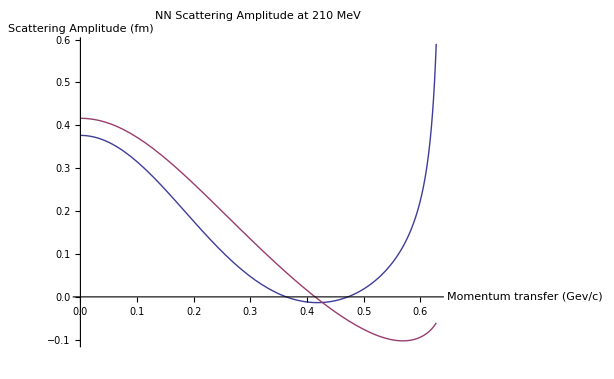

```mathematica
Plot[{Re[f[q]],Im[f[q]]},{q,0,2κ},PlotRange->All,PlotLabel->"NN Scattering Amplitude at 210 MeV",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

Γalt is the profile function if the scattering amplitude is fitted to a Gaussian. Γ and Γalt look quite different (Γalt looks like a moving average of Γ), but the eikonal potentials calculated from each are similar.

```mathematica
Γalt[b_]:=σ1 Exp[-b^2/(4 β)]
```

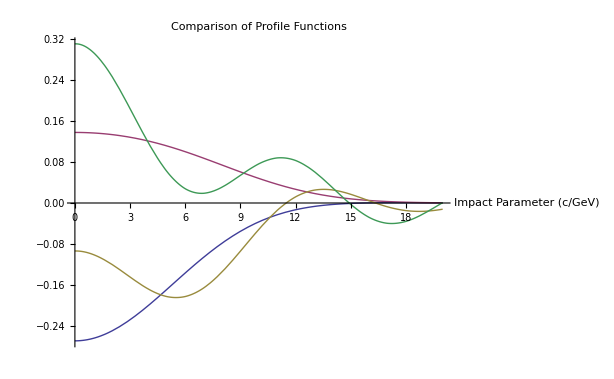

```mathematica
Plot[{Re[Γalt[b]],Im[Γalt[b]],Re[Γ[b]],Im[Γ[b]]},{b,0,20},PlotRange->All,PlotLabel->"Comparison of Profile Functions",AxesLabel->{"Impact Parameter (c/GeV)",""}]
```

```mathematica
Ualttemp[q_]:=2 Pi I NIntegrate[b BesselJ[0,q b] Log[1-Γalt[b]],{b,0,Infinity}]
```

```mathematica
Ualt=Interpolation[Table[{q,Ualttemp[q]},{q,0,1,.1}]];
```

Below is a comparison of the exact eikonal potential multiplied by the density with the eikonal potential calculated by approximating the scattering amplitude by a Gaussian.

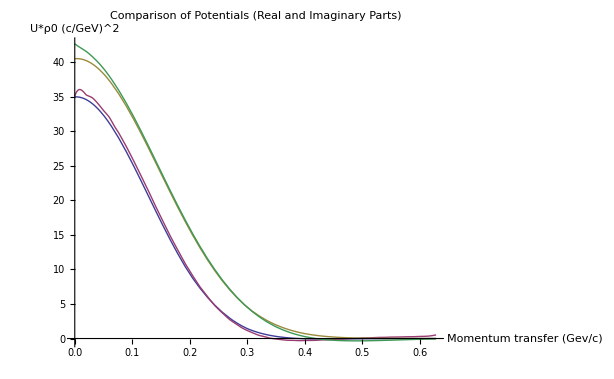

```mathematica
Plot[{Re[Ualt[q]ρ0[q]],Re[U[q] ρ0[q]],Im[Ualt[q] ρ0[q]],Im[U[q] ρ0[q]]},{q,0,2 κ},PlotLabel->"Comparison of Potentials (Real and Imaginary Parts)",AxesLabel->{"Momentum transfer (Gev/c)","U*ρ0 (c/GeV)^2"}]
```

This is the absolute difference in each of the two above graphs:

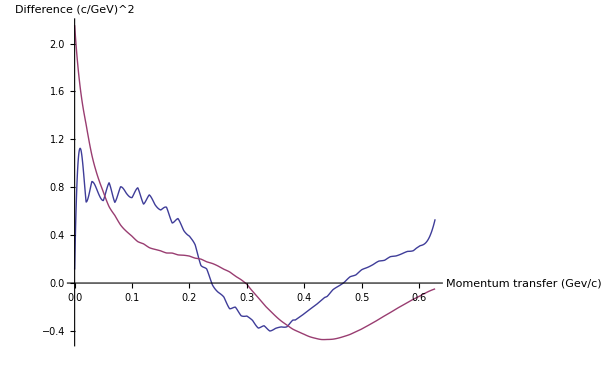

```mathematica
Plot[{Re[(U[q]-Ualt[q]) ρ0[q]],Im[(U[q]-Ualt[q]) ρ0[q]]},{q,0,2 κ},AxesLabel->{"Momentum transfer (Gev/c)","Difference (c/GeV)^2"}]
```

```mathematica
Log[U[0]]-Log[U[0.01]]
```

-0.00416047+0.0195234 ⅈ

I used the next few graphs to help me get the parameters for the Gaussian fit to U.

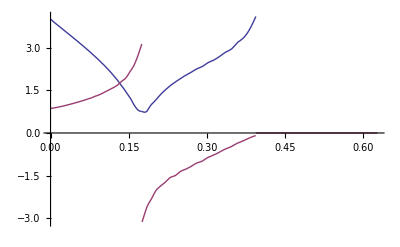

```mathematica
Plot[{Re[Log[U[Sqrt[q]]]],Im[Log[U[Sqrt[q]]]]},{q,0,2 κ}]
```

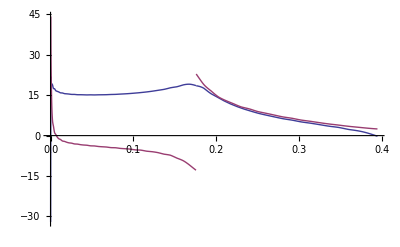

```mathematica
Plot[{Re[(Log[U[Sqrt[0]]]-Log[U[Sqrt[q]]])/q],Im[(Log[U[Sqrt[0]]]-Log[U[Sqrt[q]]])/q]},{q,0,4κ^2}]
```

```mathematica
γ=20 Quiet[(Log[U[0]]-Log[U[Sqrt[.05]]])]
```

15.1215-3.81234 ⅈ

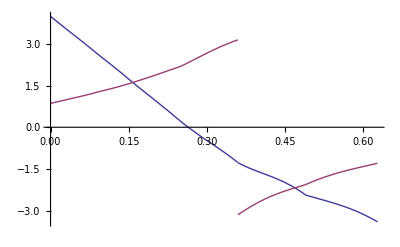

```mathematica
Plot[{Re[Log[Ualt[Sqrt[q]]]],Im[Log[Ualt[Sqrt[q]]]]},{q,0,2κ}]
```

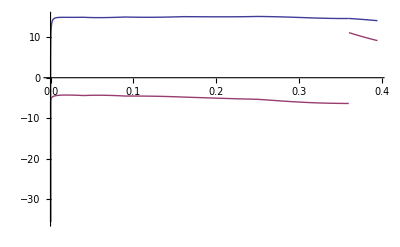

```mathematica
Plot[{Re[(Log[Ualt[Sqrt[0]]]-Log[Ualt[Sqrt[q]]])/q],Im[(Log[Ualt[Sqrt[0]]]-Log[Ualt[Sqrt[q]]])/q]},{q,0,4κ^2}]
```

```mathematica
γalt=(Log[Ualt[Sqrt[0]]]-Log[Ualt[Sqrt[.04]]])/.04
```

14.888-4.38789 ⅈ

```mathematica
Z=U[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

0.967339+0.051727 ⅈ

```mathematica
Zalt=Ualt[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

0.938188+0.0276895 ⅈ

Below is the comparison of U calculated using no approximations, and U calculated with a gaussian scattering amplitude and then fitted to a Gaussian itself.

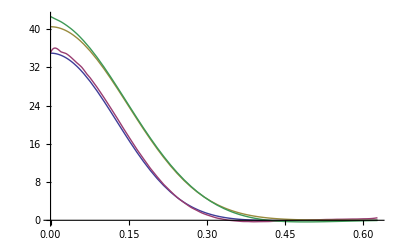

```mathematica
Plot[{Re[-I 4 Pi β σ1 Zalt Exp[-γalt q^2]ρ0[q]],Re[U[q] ρ0[q]],Im[-I 4 Pi β σ1 Zalt Exp[-γalt q^2] ρ0[q]],Im[U[q] ρ0[q]]},{q,0,2 κ},PlotLabel->"Comparison of Potentials (Real and Imaginary Parts)",AxesLabel->{"Momentum transfer (Gev/c)","U*ρ0 (c/GeV)^2"}]
```

Below is the difference between the lines in the above plot.

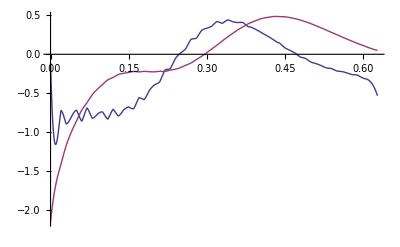

```mathematica
Plot[{Re[-I 4 Pi β σ1 Zalt Exp[-γalt q^2]ρ0[q]]-Re[U[q] ρ0[q]],Im[-I 4 Pi β σ1 Zalt Exp[-γalt q^2] ρ0[q]]-Im[U[q] ρ0[q]]},{q,0,2 κ}]
```

This is a graph of the fractional error from making these approximations.

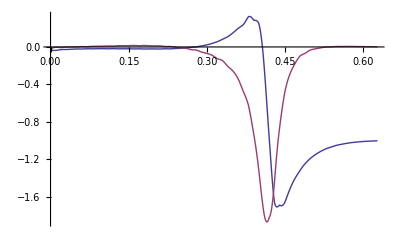

```mathematica
Plot[{Re[(-I 4 Pi β σ1 Zalt Exp[-γalt q^2]-U[q])/U[q]],Im[(-I 4 Pi β σ1 Zalt Exp[-γalt q^2]-U[q])/U[q]]},{q,0,2 κ}]
```

It looks like the errors picked up from making these approximations are probably minimal. They might affect the corrections slightly, but I have a hard time